```mathematica
$HistoryLength=0;
SetDirectory[NotebookDirectory[]];
Do[SetOptions[x,{PlotRange->Full,ImageSize->Medium,PlotTheme->"Scientific",BaseStyle->FontSize->15}],{x,{ListLinePlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot}}]
Do[SetOptions[x,{PlotRange->Full,ImageSize->Medium,PlotTheme->"Scientific",BaseStyle->FontSize->15,ExclusionsStyle->Automatic}],{x,{Plot,LogPlot,LogLogPlot}}]
```

```mathematica
compl2Interpret[x_]:=ToExpression[StringReplace[#,{"e"->" 10^","i"->" I"}]]&/@#&/@x
complInterpret[x_]:=ToExpression[StringReplace[#,{"e"->" 10^","i"->" I"}]]&/@x
xx=100000;
refSym=(compl2Interpret@Import["srcSymData.csv","CSV"])[[xx;;-xx]];
srcPermBitData = Import["srcPermBitData.csv","CSV"];
distSym = (compl2Interpret@Import["eqSymOutData.csv","CSV"])[[xx;;-xx]];
```

```mathematica
ComplexListPlot[{eqSymOutData[[;;,1]],srcSymData[[;;,1]]},PlotStyle->{PointSize[0.006],PointSize[0.02]}]
```

-Graphics-

```mathematica
ComplexListPlot[{eqSymOutData[[;;,1]]-srcSymData[[;;,1]]},PlotStyle->PointSize[0.002],Joined->True]
```

-Graphics-

```mathematica
Length[srcPermBitData]
```

1036288

```mathematica
Length[srcSymData]
```

259072

```mathematica
Length[srcSymData[[xx;;-xx]]]
```

258874

```mathematica
Export["srcSymDataMod.txt",{Re[#[[1]]],Im[#[[1]]],Re[#[[2]]],Im[#[[2]]]}&/@srcSymData[[xx;;-xx]],"Table"]
```

srcSymDataMod.txt

```mathematica
Export["eqSymOutDataMod.txt",{Re[#[[1]]],Im[#[[1]]],Re[#[[2]]],Im[#[[2]]]}&/@eqSymOutData[[xx;;-xx]],"Table"]
```

eqSymOutDataMod.txt

```mathematica
30  679/0.3
```

67900.

```mathematica
330000/(50. 1200 3000 10^-9 2700)
```

679.012

```mathematica
Export["srcPermBitDataMod.txt",srcPermBitData,"Table"]
```

srcPermBitDataMod.txt

```mathematica
Length[srcPermBitData]
```

1036288

```mathematica
Length[srcSymData]4
```

1036288

```mathematica
tmp=Transpose@{srcSymData[[;;,1]]//Re,srcSymData[[;;,1]]//Im,(StringJoin@@(ToString/@Reverse[#]))&/@Partition[srcPermBitData[[;;,1]],4]}//DeleteDuplicates
```

{{1,-1,1111},{1,1,1011},{-1,-1,1110},{3,-3,0101},{-1,1,1010},{-3,-1,1100},{-3,1,1000},{1,-3,0111},{3,1,1001},{-3,3,0000},{3,-1,1101},{-3,-3,0100},{1,3,0011},{-1,3,0010},{3,3,0001},{-1,-3,0110}}

```mathematica
("{0b"<>#[[3]]<>","<>ToString[#[[1]]]<>"."<>If[#[[2]]>=0,"+","-"]<>ToString[Abs@#[[2]]]<>".i},\n")&/@tmp//StringJoin
```

{0b1111,1.-1.i},
{0b1011,1.+1.i},
{0b1110,-1.-1.i},
{0b0101,3.-3.i},
{0b1010,-1.+1.i},
{0b1100,-3.-1.i},
{0b1000,-3.+1.i},
{0b0111,1.-3.i},
{0b1001,3.+1.i},
{0b0000,-3.+3.i},
{0b1101,3.-1.i},
{0b0100,-3.-3.i},
{0b0011,1.+3.i},
{0b0010,-1.+3.i},
{0b0001,3.+3.i},
{0b0110,-1.-3.i},

```mathematica
479773./Length[srcPermBitData]
```

0.462973

```mathematica
479773./4
```

119943.

```mathematica
384400. 10^3/(3 30 24 3600)
```

49.4342

```mathematica
√(2. Log[2])
```

1.17741

```mathematica
Solve[(1000 +6400)10^3 x Degree == 10000000.,x]
```

{{x→77.4267}}

```mathematica
2. Pi/8
```

0.785398

```mathematica
(670 +6400.)10^3 (2 Pi)/8/1000
```

5552.77

```mathematica
3/0.5
```

6.

```mathematica
250000  2 8 2 21 21
```

3528000000

```mathematica
Length[refSym]
```

159074

```mathematica
NMSE[ref_,dist_]:=10 Log10[Total@1. Norm[dist-ref]^2/(Total@(Norm[dist]^2))]
```

```mathematica
NMSE[refSym,distSym]
```

-12.706

```mathematica
distSym
```

{{0.74963+0.74688 ⅈ,1.7763+1.4494 ⅈ},{-0.90444-1.3039 ⅈ,-0.75449+1.2107 ⅈ},{0.954+0.84685 ⅈ,1.0616-0.85259 ⅈ},159068,{-3.6502+1.0008 ⅈ,3.8894-0.73703 ⅈ},{-0.069417-3.0574 ⅈ,-1.7797+2.6365 ⅈ},{0.57169-0.29854 ⅈ,-0.86483-3.1389 ⅈ}}
 |  |  |  |

```mathematica
M=5;
```

```mathematica
len = Length[distSym];
bounded[x_]:=If[x<=1,1,If[x>=len,len,x]]
u1[k_,m_,n_]:=distSym[[bounded[k+m],1]]distSym[[bounded[k+n],1]]Conjugate[distSym[[bounded[k+m+n],1]]]
u2[k_,m_,n_]:=distSym[[bounded[k+m],1]]distSym[[bounded[k+n],2]]Conjugate[distSym[[bounded[k+m+n],2]]]
```

```mathematica
U=Table[
Flatten[Table[u1[k,m,n],{m,-M,M},{n,-M,M}]]
~Join~
Flatten[Table[u2[k,m,n],{m,-M,M},{n,-M,M}]],
{k,1,len}];
```

$Aborted

```mathematica
(2M+1)^2 2
```

242

```mathematica
modelData=Import["result.txt","Table",HeaderLines->1];
```

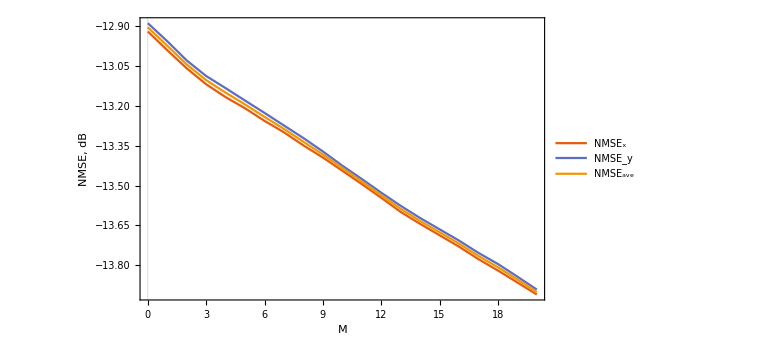

```mathematica
ListLinePlot[Transpose[{{#[[1]],#[[2]]},{#[[1]],#[[3]]},{#[[1]],#[[4]]}}&/@modelData],PlotLegends->Placed[LineLegend[{"NMSE_x","NMSE_y","NMSE_ave"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.8,0.7}],ImageSize->Large,FrameLabel->{"M","NMSE, dB"}]
```

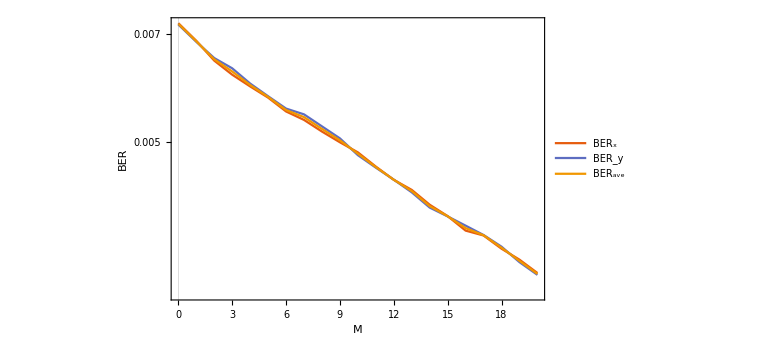

```mathematica
ListLogPlot[Transpose[{{#[[1]],#[[5]]},{#[[1]],#[[6]]},{#[[1]],#[[7]]}}&/@modelData],PlotLegends->Placed[LineLegend[{"BER_x","BER_y","BER_ave"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.8,0.7}],ImageSize->Large,FrameLabel->{"M","BER"},Joined->True]
```